### Description

This notebook imports the colony counts of wild types and mutants that were previously measured in a Luria-Delbrueck type experiment and computes the likelihood of mutation rate and fitness difference using a simple growth-mutation simulation.

### Import experiment data

```mathematica
SetDirectory[NotebookDirectory[]];
dox0=Import["colony counter dox=0.csv","Data"][[2;;-1]];
dox0=Select[dox0,NumberQ@First@#&];
dox1=Import["colony counter dox=1.csv","Data"][[2;;-1]];
dox1=Select[dox1,NumberQ@First@#&];
exp1=dox1[[All,2]]/dox1[[All,3]];
exp0=dox0[[All,2]]/dox0[[All,3]];
```

### Simulate growth process

The simulation is simple: start with a small, random number of cells. Each cell divides at rate kWT, mutates at rate μ. The mutants grow at rate kMT. Grow all cells for 7-8 generation (in accord with experiment). Repeat 50000 times for each set of parameters (kMT, μ).

```mathematica
kWT=1;
μ=0.5 10^-2;
kMT=1.;
dt=1;
repeats=50000;

mList=10^-3 Range[1,16,1];
hist=Table[0,{Length@mList}];
kList=Range[0.7,1.3,0.05];
hist2=Table[0,{Length@kList}];
Monitor[For[k=1,k≤Length@kList,k++,{kMT=kList[[k]],For[m=1,m≤Length@mList,m++,{μ=mList[[m]],n2=Table[0,{repeats}];For[i=1,i≤repeats,i++,{
n0=RandomVariate[PoissonDistribution[2]];
x=n0;
y=0;
For[t=1,t≤8,t+=dt,{
If[t==8&&RandomReal[]>0.7,
x+=If[x>0,RandomVariate[PoissonDistribution[x kWT dt]],0];
y+=If[y>0,RandomVariate[PoissonDistribution[y kMT dt]],0]+If[x>0,RandomVariate[PoissonDistribution[x μ dt]],0]],
If[t<8,x+=If[x>0,RandomVariate[PoissonDistribution[x kWT dt]],0];
y+=If[y>0,RandomVariate[PoissonDistribution[y kMT dt]],0]+If[x>0,RandomVariate[PoissonDistribution[x μ dt]],0]]
}];
n2[[i]]={x,y};
}],
hist[[m]]=n2}],
hist2[[k]]=Table[{#[[All,2]],#[[All,1]]}&@DeleteCases[hist[[i]],{0,0},2],{i,1,Length@hist}];
}],{k,m,i}];
```

#### smooth noisy histograms

```mathematica
Monitor[interp=Table[Interpolation[Join[#,Table[{#[[-1,1]]+0.01 k,0},{k,1,(1-#[[-1,1]])/0.01}]]&@(Transpose[{MeanFilter[Most@#[[1]],0],MeanFilter[#[[2]],0]}]&@HistogramList[(hist2[[i,j,1]]/hist2[[i,j,2]]),{0.01},"PDF"]),InterpolationOrder->1],{i,1,Length@kList},{j,1,Length@mList}];,i]
```

### Compute likelihood

```mathematica
Lestimator1=Table[Total@Log@(ReplaceAll[interp[[i,j]][exp1]/. {x_/;x<0->0.},0.->Min[Select[#,#>0&]]])&@interp[[i,j]][exp1],{i,1,Length@kList},{j,1,Length@mList}];
Lestimator0=Table[Total@Log@(ReplaceAll[interp[[i,j]][exp0]/. {x_/;x<0->0.},0.->Min[Select[#,#>0&]]])&@interp[[i,j]][exp0],{i,1,Length@kList},{j,1,Length@mList}];
Lestimator1=Table[{kList[[i]],mList[[j]],(Lestimator1[[i,j]])},{i,1,Length@kList},{j,1,Length@mList}];
Lestimator0=Table[{kList[[i]],mList[[j]],(Lestimator0[[i,j]])},{i,1,Length@kList},{j,1,Length@mList}];
```

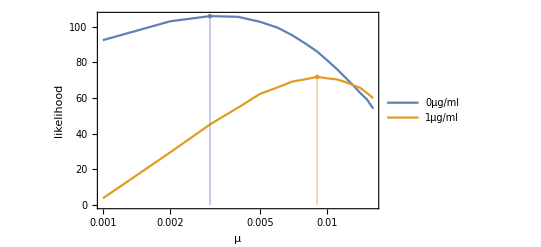

0.003

0.00055314

0.009

0.000679476

```mathematica
Show[ListLogLinearPlot[{Lestimator0[[-1]][[All,{2,3}]],Lestimator1[[6]][[All,{2,3}]]},Joined->True,FrameLabel->{"μ","likelihood"}(*,GridLines->{{0.003,0.009},None}*),PlotRangePadding->{{None,None},{0Scaled@0.05,Scaled@0.05}},PlotLegends->Placed[{"0μg/ml","1μg/ml"},Scaled@{0.18,0.6}]],ListLogLinearPlot[{{{0.003,106.02293051997309}},{{0.009,71.91934355216623}}},Filling->Bottom,PlotRange->{{0.001,0.03},{0,110}}]]
mu0=0.003
mu0err=1/Abs@√(Interpolation[(Lestimator0[[-1]][[All,{2,3}]])]''[0.003])
mu1=0.009
mu1err=1/Abs@√(Interpolation[(Lestimator1[[6]][[All,{2,3}]])]''[0.009])
```